```mathematica
iSkew = -Graphics-;
```

```mathematica
-Graphics-//ImageData//Dimensions
```

{302,346}

```mathematica
ImageLines[-Graphics-]
```

{{{346.,162.39},{260.359,302.}},{{0.,149.039},{247.64,302.}},{{346.,157.583},{94.3498,0.}},{{0.,135.774},{83.2887,0.}}}

```mathematica
-Graphics-//Show[#,Graphics[{Red,Line/@ImageLines[#]}]]&
```

-Graphics-

```mathematica
Show[iSkew, Graphics[{Red, Thick, Line[{{0,149.03},{247.64,302}}]}]]
```

-Graphics-

```mathematica
Cases[Normal@Show[ Graphics[{Red, Thick, Line[{{0,149.03},{247.64,302}}]}]],
Line[x_]:>x[[2]]-x[[1]], Infinity]
```

{{247.64,152.97}}

```mathematica
VectorAngle[%[[1]],{1,0}]
```

0.553341

```mathematica
points={{0,149.03},{247.64,302}}
```

{{0,149.03},{247.64,302}}

```mathematica
points[[2]]-points[[1]]
```

{247.64,152.97}

```mathematica
VectorAngle[%,{1,0}]
```

0.553341

```mathematica
VectorAngle[%[[1]],{1,0}]
```

Part::partd: Part specification 0.553341 ⟦ 1 ⟧ is longer than depth of object.

VectorAngle[0.553341⟦1⟧,{1,0}]

```mathematica
-Graphics-//ImageRotate[#, -0.5533407484623032]&
```

-Graphics-

```mathematica
On[Assert];
```

```mathematica
Assert[1>1];
```

Assert::asrtf: Assertion 1 > 1 failed.

```mathematica
-Graphics-//Erosion[#,{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}]&
```

-Graphics-

```mathematica
-Graphics-//Show[#,Graphics[{Red,Line/@ImageLines[#]}]]&
```

-Graphics-

```mathematica
-Graphics-//ImageLines[#]&//Part[#,1]&
```

{{0.,203.556},{767.,312.283}}

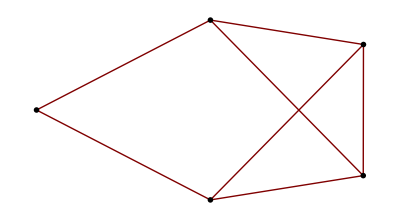

```mathematica
imgs=ExampleData/@ExampleData["TestImage"];
GraphPlot[{1->4,1->5,2->3,2->4,2->5,3->4,3->5},VertexRenderingFunction->(Inset[Image[imgs[[#2]],ImageSize->100],#1]&)]
```

(*Deleting small components from a label matrix:*)

```mathematica
SelectComponents[ ({{1, 1, 1, 0}, {1, 1, 1, 0}, {1, 1, 1, 0}, {0, 2, 2, 2}}),"Count",#> 5&]//MatrixForm
```

(1 | 1 | 1 | 0
1 | 1 | 1 | 0
1 | 1 | 1 | 0
0 | 0 | 0 | 0)